```mathematica
BordersUnsorted[f_]:=Module[{edgs},
  edgs=Flatten[Map[{
   {Part[#,1],Part[#,2]},
   {Part[#,2],Part[#,3]},
   {Part[#,3],Part[#,1]},
   {Part[#,2],Part[#,1]},
   {Part[#,3],Part[#,2]},
  {Part[#,1],Part[#,3]}
  }&,f],1];
DeleteDuplicates[Flatten[Part[Select[Tally[edgs],Last[#]==1&],;;,1]]]
];
```

```mathematica
AngleDefect[objfile_,returnOnlyInner_:True]:=Module[{brd,inner,angleDefect,input,v,f},
input=Import[objfile,"GraphicsComplex"];
v=Part[input,1];
Clear[x];
f=Flatten[Cases[input,Triangle[x_]->x,Infinity],1];
brd=BordersUnsorted[f];
inner=Complement[Range[Length[v]],brd];
angleDefect=ConstantArray[-2π,Length[v]];

Map[Function[fi,
Table[
Module[{a,k1,k2,e1,e2},
k1=Mod[k,3]+1;
k2=Mod[k+1,3]+1;
e1=Part[v,Part[fi,k1]]-Part[v,Part[fi,k]];
e2=Part[v,Part[fi,k2]]-Part[v,Part[fi,k]];
a=ArcCos[e1.e2/ (Norm[e1] *Norm[e2])];
Part[angleDefect,Part[fi,k]] +=a;
],{k,3}]
],f];

Part[angleDefect,brd]=.0;
If[returnOnlyInner,Part[angleDefect,inner],angleDefect]
];
```

```mathematica
file="/Users/ph/Documents/Projects/DevelopableStitching/data/new/side11_40/out.obj";
ad=Abs[AngleDefect[file]];
```

0.000231078

9.3855×10^-8

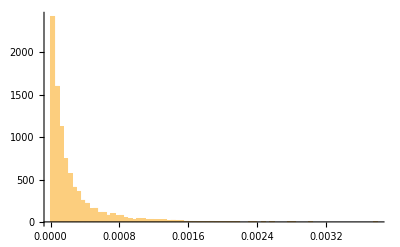

```mathematica
Mean[ad]
Variance[ad]
Histogram[ad,PlotRange->All]
```

```mathematica
ad2=Abs[AngleDefect[file,False]];
```

```mathematica
input=Import[file,"GraphicsComplex"];
v=Part[input,1];
f=Flatten[Cases[input,Triangle[x_]->x,Infinity],1];
cl=ColorData["BlueGreenYellow"]/@(0.1+0.9Rescale[ad2]);
```

```mathematica
Graphics3D[
{
EdgeForm[],
GraphicsComplex[v,Polygon[f],VertexColors->cl]
},Boxed->False
]
```

-Graphics3D-